Constants

```mathematica
QE=1.6 10^-19;EPSILON0=8.85 10^-12;c=3 10^8;
```

Functions

```mathematica
gamma[Ek_]:=Ek/0.511+1;beta[Ek_]:=√(1-1/gamma[Ek]^2);v[Ek_]:=beta[Ek]*c;
R[Ek_,d_,t_]:=√(d^2+v[Ek]^2 t^2);
```

Single Electron

```mathematica
Ex[Ek_,d_,t_]:=-(QE*(1-beta[Ek]^2))/(4*π*EPSILON0)*(d/R[Ek,d,t]^3)/((1-beta[Ek]^2 d^2/R[Ek,d,t]^2)^(3/2));
```

```mathematica
Exmax[Ek_,d_]:=-(QE*gamma[Ek])/(4*π*EPSILON0*d^2);τE[Ek_,d_]:=2(2^(2/3)-1)^(1/2)d/gamma[Ek]/v[Ek];
```

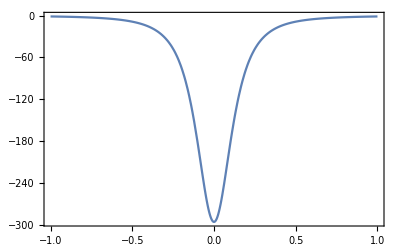

```mathematica
Plot[10^10 Ex[10,1,t],{t,-10^-9,10^-9},PlotRange->All,Frame->True]
```

rect micro-pulse

```mathematica
N0=10^10;
```

```mathematica
Erectmx[Ek_,d_,τ0_,t_]:=-(N0*QE*gamma[Ek])/(4*π*EPSILON0*d^2)*((τ0+t)/(2*τ0)*1/(√(1+beta[Ek]^2*gamma[Ek]^2*c^2*(τ0+t)^2/d^2))+(τ0-t)/(2*τ0)*1/(√(1+beta[Ek]^2*gamma[Ek]^2*c^2*(τ0-t)^2/d^2)));
Erectmz[Ek_,d_,τ0_,t_]:=-(N0*QE)/(4*π*EPSILON0*d^2)*(d/c)/(2*beta[Ek]*gamma[Ek]*τ0)*(1/(√(1+beta[Ek]^2*gamma[Ek]^2*c^2*(τ0-t)^2/d^2))-1/(√(1+beta[Ek]^2*gamma[Ek]^2*c^2*(τ0+t)^2/d^2)));
Erectmax[Ek_,d_,τ0_]:=-(N0*QE*gamma[Ek])/(4*π*EPSILON0*d^2)*1/(√(1+beta[Ek]^2*gamma[Ek]^2*τ0^2*v[Ek]^2/d^2));
τrectm[Ek_,d_,τ0_]:=2*τ0+2*τ0*((1+4*beta[Ek]^2*gamma[Ek]^2*τ0^2*v[Ek]^2/d^2)/((1+4*beta[Ek]^2*gamma[Ek]^2*τ0^2*v[Ek]^2/d^2)^(3/2)-1))*(2-√((1+4*beta[Ek]^2*gamma[Ek]^2*τ0^2*v[Ek]^2/d^2)/(1+beta[Ek]^2*gamma[Ek]^2*τ0^2*v[Ek]^2/d^2)));
```

```mathematica
(*
Integrate[1/(2a)*DirichletWindow[x/(2a)]*1/((1+b^2(x+c0)^2)^(3/2)),{x,-∞,∞},Assumptions->{a∈Reals&&a>0&&b∈Reals&&b>0&&c0∈Reals&&c0>0}];
Integrate[b/(2a)*DirichletWindow[x/(2a)]*(x+c0)/((1+b^2(x+c0)^2)^(3/2)),{x,-∞,∞},Assumptions->{a∈Reals&&a>0&&b∈Reals&&b>0&&c0∈Reals&&c0>0}];
*)
```

gaussian micro-pulse

```mathematica
Solve[Integrate[A*Exp[-x^2/τ0^2],{x,-2τ0,2τ0},Assumptions->{τ0∈Reals&&τ0>0&&A∈Reals&&A>0}]==eN/v0,A]
```

{{A→eN/(√π v0 τ0 Erf[2])}}

```mathematica
Egaussx[Ek_,d_,τ0_,t_]:=-(N0*QE*gamma[Ek])/(4*π*EPSILON0*d^2)*1/(√π τ0*Erf[2])*NIntegrate[Exp[-x^2/τ0^2]*1/((1+beta[Ek]^2*gamma[Ek]^2*c^2*(x+t)^2/d^2)^(3/2)),{x,-2τ0,2τ0}];
```

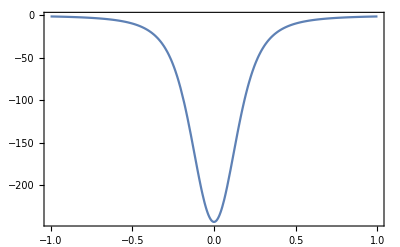

```mathematica
Plot[Egaussx[10,1,100 10^-12,t],{t,-10^-9,10^-9},PlotRange->All,Frame->True]
```